# Fusc

Evaluate the fusc function

## Definition

```mathematica
ClearAll[Fusc]
```

```mathematica
Attributes[Fusc]={Listable,NumericFunction};

Fusc[0]:=0;

Fusc[1]:=1;

Fusc[n_Integer?(EvenQ[#]&&#>0&)]:=Fusc[n/2];

Fusc[n_Integer?(OddQ[#]&&#>0&)]:=Module[{
	m=(n-1)/2
},

	Return[Fusc[m]+Fusc[m+1]];
]
```

## Documentation

### Usage

Fusc[n]

gives the fusc function fusc(n).

### Details & Options

Integer mathematical function, suitable for both symbolic and numerical manipulation.

Fusc is defined by the recurrence relation fusc(0)=0, fusc(1)=1, fusc(2m)=fusc(m) and fusc(2m+1)=fusc(m)+fusc(m+1).

The fusc function is also known as Stern’s Diatomic Series.

According to author Edsger W. Dijkstra (EWD 570), the fusc function is named for the obfuscated appearance of its output.

Fusc automatically threads over lists.

## Examples

### Basic Examples

Evaluate numerically for positive even integer input:

```mathematica
Fusc[12]
```

2

Evaluate numerically for positive odd integer input:

```mathematica
Fusc[31]
```

5

Plot Fusc over a subset of the non-negative integers:

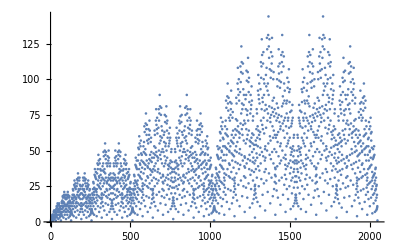

```mathematica
ListPlot[Table[Fusc[n],{n,0,2048}]]
```

### Scope

Fusc threads elementwise over lists:

```mathematica
Fusc[{3,5,11,21,162,247000000}]
```

{2,3,5,8,14,7241}

### Applications

The value fusc(n+1) is the number of odd binomial coefficients of the form Binomial[n-r,r], 0≤2r≤n:

```mathematica
fuscs=Table[Fusc[n+1],{n,0,100}]
```

{1,1,2,1,3,2,3,1,4,3,5,2,5,3,4,1,5,4,7,3,8,5,7,2,7,5,8,3,7,4,5,1,6,5,9,4,11,7,10,3,11,8,13,5,12,7,9,2,9,7,12,5,13,8,11,3,10,7,11,4,9,5,6,1,7,6,11,5,14,9,13,4,15,11,18,7,17,10,13,3,14,11,19,8,21,13,18,5,17,12,19,7,16,9,11,2,11,9,16,7,19}

```mathematica
bins=Table[Length@Select[Table[Binomial[n-r,r],{r,0,n,2}],OddQ[#]&],{n,0,200,2}]
```

{1,1,2,1,3,2,3,1,4,3,5,2,5,3,4,1,5,4,7,3,8,5,7,2,7,5,8,3,7,4,5,1,6,5,9,4,11,7,10,3,11,8,13,5,12,7,9,2,9,7,12,5,13,8,11,3,10,7,11,4,9,5,6,1,7,6,11,5,14,9,13,4,15,11,18,7,17,10,13,3,14,11,19,8,21,13,18,5,17,12,19,7,16,9,11,2,11,9,16,7,19}

Confirm the two lists are equal:

```mathematica
fuscs==bins
```

True

An alternative way to compute the same quantity:

```mathematica
bins2=Count[#,_?(OddQ[#]&)]&/@Table[Binomial[n-r,r],{n,0,200,2},{r,0,n,2}]
```

{1,1,2,1,3,2,3,1,4,3,5,2,5,3,4,1,5,4,7,3,8,5,7,2,7,5,8,3,7,4,5,1,6,5,9,4,11,7,10,3,11,8,13,5,12,7,9,2,9,7,12,5,13,8,11,3,10,7,11,4,9,5,6,1,7,6,11,5,14,9,13,4,15,11,18,7,17,10,13,3,14,11,19,8,21,13,18,5,17,12,19,7,16,9,11,2,11,9,16,7,19}

Confirm all three are equal:

```mathematica
fuscs==bins==bins2
```

True

### Possible Issues

Fusc returns unevaluated if its input is anything other than a non-negative integer:

```mathematica
{Fusc[-1],Fusc[22/7],Fusc[Pi],Fusc[2.0],Fusc[blah]}
```

{Fusc[-1],Fusc[22/7],Fusc[π],Fusc[2.],Fusc[blah]}

### Neat Examples

Generate the first 100 terms of Stern's diatomic series, also known as the Stern–Brocot sequence (OEIS A002487):

```mathematica
Fusc/@Range[0,99]
```

{0,1,1,2,1,3,2,3,1,4,3,5,2,5,3,4,1,5,4,7,3,8,5,7,2,7,5,8,3,7,4,5,1,6,5,9,4,11,7,10,3,11,8,13,5,12,7,9,2,9,7,12,5,13,8,11,3,10,7,11,4,9,5,6,1,7,6,11,5,14,9,13,4,15,11,18,7,17,10,13,3,14,11,19,8,21,13,18,5,17,12,19,7,16,9,11,2,11,9,16}

When used in conjunction with Prime, you can generate OEIS sequences A261179 and A261273:

```mathematica
Fusc[#]&/@(Prime[#]&/@Range[1,100])
```

{1,2,3,3,5,5,5,7,7,7,5,11,11,13,9,13,11,9,11,13,15,13,19,17,11,19,17,21,19,13,7,13,19,23,29,25,23,25,27,31,29,31,13,13,25,23,31,17,23,27,25,19,17,17,9,19,27,21,37,31,35,41,41,37,33,29,49,37,49,41,27,41,33,41,31,15,31,39,33,41,41,49,37,35,41,39,19,37,41,31,43,23,31,37,27,23,15,27,33,37}

```mathematica
Fusc[#+1]&/@(Prime[#]&/@Range[1,100])
```

{2,1,2,1,2,3,4,3,2,4,1,7,8,5,2,8,4,5,5,4,11,3,8,12,9,12,5,8,11,10,1,6,14,9,18,7,13,11,8,18,12,19,2,11,16,7,13,3,10,17,18,4,13,6,8,6,16,5,23,22,13,26,17,10,23,16,19,29,18,23,22,12,7,25,11,2,20,23,26,29,18,31,8,27,11,14,16,27,24,7,18,4,9,14,11,6,8,20,13,21}

These two sequences combine to form the prime numbered elements in the Calkin–Wilf sequence, one popular enumeration of the rational numbers. More precisely, the terms of the Calkin–Wilf enumeration of the rationals are given by fusc(n)/fusc(n+1):

```mathematica
Table[Fusc[n]/Fusc[n+1],{n,0,50}]
```

{0,1,1/2,2,1/3,3/2,2/3,3,1/4,4/3,3/5,5/2,2/5,5/3,3/4,4,1/5,5/4,4/7,7/3,3/8,8/5,5/7,7/2,2/7,7/5,5/8,8/3,3/7,7/4,4/5,5,1/6,6/5,5/9,9/4,4/11,11/7,7/10,10/3,3/11,11/8,8/13,13/5,5/12,12/7,7/9,9/2,2/9,9/7,7/12}

## Source & Additional Information

### Contributed By

Christopher Stover

### Keywords

fusc function

obfuscate

enumeration of the rationals

stern's diatomic sequence

calkin-wilf tree

dijkstra

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

Binomial

### Related Resource Objects

Collatz

### Source/Reference Citation

Dijkstra, E. W., Selected Writings on Computing: A Personal Perspective, EWD570 and EWD578. New York: Springer-Verlag, 1982.

### Links

Wikipedia–Calkin–Wilf tree: Stern's diatomic sequence

Fusc Function–Wolfram MathWorld

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.